```mathematica
SetDirectory["C:\\Users\\nanma\\Documents\\GitHub\\hyperbolic_tiling"];
```

```mathematica
maxExplosionFactor=10.0;
frameCount=150;

maxExplosionFactor=8.0;
frameCount=6;

cellThreshold=10;
(*cellThreshold=40;*)

argv=Rest@$ScriptCommandLine;
If[Length[argv]<3,Print["Usage: wolframscript.exe explode_honeycomb.wls <p> <q> <r> <cellThreshold>"];];

If[Length[argv]>=3,p=ToExpression[argv[[1]]];q=ToExpression[argv[[2]]];r=ToExpression[argv[[3]]],p=7;q=3;r=3;];

If[Length[argv]>=4,cellThreshold=ToExpression[argv[[4]]]];

Print["{"<>IntegerString[p]<>", "<>IntegerString[q]<>", "<>IntegerString[r]<>"}"];
shape="explode_"<>ToString[p,InputForm]<>"_"<>ToString[q,InputForm]<>"_"<>ToString[r,InputForm];

dataFolder="data";
imageFolder="images";
epsilon=0.00000001;
imageSize={4,3}/3*720;
lighting={{"Point",White,{10,-10,10}*5}};
rangeFactor=1.25;
colors=Join[{Red,Blue,Green,Yellow,Magenta,LightCyan,Brown,Orange,Pink,Darker[Gray,0.2],Cyan},RandomColor[80]];

outputFolder=FileNameJoin[{imageFolder,"explode_honeycombs"}];
If[!DirectoryQ[outputFolder],CreateDirectory[outputFolder]];
exportToPov=True;
splitEdgeParts=15;

Needs["POVRayRender`"];
ConfigurePOVRayRender["POVRayPath"->"C:\\Program Files\\POV-Ray\\v3.7\\bin\\pvengine64.exe"];

phi=(1+Sqrt[5])/2;
splitEdge[edge_,n_]:=Table[{k edge[[1]]+(1-k) edge[[2]],(k+1/n) edge[[1]]+(1-k-1/n) edge[[2]]},{k,0,1-1/n,1/n}];
splitFaceToTriangles[face_]:=Table[{face[[1]],face[[k-1]],face[[k]]},{k,3,Length[face]}];
HInner[v_,u_]:=2*v[[1]]*u[[1]]-Dot[v,u];
HNormSquare[v_]:=HInner[v,v];
HNorm[v_]:=Sqrt[HNormSquare[v]];
HNormalize[v_,norm_]:=v/HNorm[v]*norm;
Rotation[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}};

cellCenterToOrigin=ArrayFlatten[{{1,0},{0,RotationMatrix[{-{1,1,1},{1,0,0}}]}}];
Boost[boost_]:={{Cosh[boost],Sinh[boost],0,0},{Sinh[boost],Cosh[boost],0,0},{0,0,1,0},{0,0,0,1}};

HReflect[point_,mirror_]:=point-2*HInner[point,mirror]/HInner[mirror,mirror]*mirror;
centralReflect[point_,mirror_]:=-HReflect[point,mirror];
HDoubleReflect[point_,mirror1_,mirror2_]:=HReflect[HReflect[point,mirror1],mirror2];
ApproxSamePoint[point1_,point2_]:=Round[point1,epsilon]==Round[point2,epsilon];
ApproxSamePointLoose[point1_,point2_]:=Round[point1,10 epsilon]==Round[point2,10 epsilon];

getEdgesFromFace[face_]:=Table[{face[[i+1]],face[[Mod[i+1,Length[face]]+1]]},{i,0,Length[face]-1}];
sameCenter[set1_,set2_]:=ApproxSamePoint[Mean[N[set1]],Mean[N[set2]]];
sameCellCenter[cell1_,cell2_]:=sameCenter[Flatten[cell1,1],Flatten[cell2,1]];
getCellCenter[cell_]:=Total[Flatten[cell,1]]/Length[Flatten[cell,1]];
getCellHeight[cell_]:=getCellCenter[cell][[1]];
opaqueFactor=2/3;
getOpacityByExplosion[factor_]:=If[factor<maxExplosionFactor*opaqueFactor,1,1/(1-opaqueFactor)-1/(1-opaqueFactor)/maxExplosionFactor*factor];

getSplitEdges[edges_]:=Module[{splitEdges,eid,edge,norm,splitParts},splitEdges={};
For[eid=1,eid<=Length[edges],eid++,edge=edges[[eid]];
norm=HNorm[edge[[1]]];
splitParts=splitEdge[edge,splitEdgeParts];
splitParts=Map[HNormalize[#,norm]&,splitParts,{2}];
splitEdges=Join[splitEdges,splitParts];];
splitEdges];

getHyperboloid[v_]:={v[[2]],v[[3]],v[[4]]};
getKlein[v_]:={v[[2]],v[[3]],v[[4]]}/v[[1]];
getPoincare[v_]:={v[[2]],v[[3]],v[[4]]}/(1+v[[1]]);
getPoincareExploded[v_,norm_]:=norm {v[[2]],v[[3]],v[[4]]}/(norm+v[[1]]);
explodedCell[cell_,explosionFactor_]:=Map[(#+Mean[Map[Mean,cell]]*(HNorm[First[First[cell]]]/HNorm[Mean[Map[Mean,cell]]])^1.5*explosionFactor)&,cell,{2}];

explodeCellsByStep[cells_,refCellCenters_,explosionFactor_,explosionStep_,heightsMap_]:=Module[{inactiveCells,activeCells},If[explosionStep==0,inactiveCells={};
activeCells=cells,If[explosionStep==2,inactiveCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&];
activeCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]==0&],(*explosionStep==1*)inactiveCells=Select[cells,Norm[getCellCenter[#][[Range[2,4]]]]<epsilon&];
activeCells=Select[cells,Norm[getCellCenter[#][[Range[2,4]]]]>epsilon&&Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&]
(*inactiveCells={};*)
(*activeCells=Select[cells,Length[Intersection[{getCellCenter[#]},refCellCenters,SameTest->ApproxSamePoint]]>0&];*)];];
For[acId=1,acId<=Length[activeCells],acId++,cell=activeCells[[acId]];
height=getCellHeight[cell];
layer=heightsMap[Round[height,epsilon]];
nonlinearFactor=getNonlinearFactor[explosionFactor,layer];
Print["{acId, nonlinearFactor, layer}"];
Print[{acId,nonlinearFactor,layer}];
activeCells[[acId]]=explodedCell[cell,nonlinearFactor];];
(*activeCells=Map[explodedCell[#,explosionFactor]&,activeCells];*){activeCells,inactiveCells}];


filterCells[cells_,cellThreshold_]:=Module[{cellCenterHeights,heightTally,tallyCounts,includeCount,heightThreshold,levelIndex},cellCenterHeights=Map[getCellHeight,cells];
heightTally=Tally[cellCenterHeights,ApproxSamePoint]//Sort;
tallyCounts=Map[#[[2]]&,heightTally];
Print[tallyCounts];
includeCount=0;
heightThreshold=-1;
For[levelIndex=1,levelIndex<=Length[heightTally],levelIndex++,If[includeCount<cellThreshold,includeCount+=heightTally[[levelIndex]][[2]];
If[includeCount>=cellThreshold,heightThreshold=heightTally[[levelIndex]][[1]]+epsilon];];];
If[heightThreshold==-1,heightThreshold=heightTally[[Length[heightTally]]][[1]]+epsilon];
filteredCells=Select[cells,getCellCenter[#][[1]]<=heightThreshold&];
Print["Filter from "<>IntegerString[Length[cells]]<>" cells down to "<>IntegerString[Length[filteredCells]]<>" cells."];
filteredCells];

getNonlinearFactor[linear_,layer_]:=Module[{layerOffset,linearOffset,returnValue},layerOffset=If[layer>1,layer-1,0];
linearOffset=linear+layerOffset*delayFactor;
returnValue=linearOffset^2/maxExplosionFactor;
(*If[returnValue>maxExplosionFactor,returnValue=maxExplosionFactor];*)If[linearOffset<0,returnValue=0];
returnValue];

dataFileName=FileNameJoin[{dataFolder,"hyper_"<>ToString[p,InputForm]<>"_"<>ToString[q,InputForm]<>"_"<>ToString[r,InputForm]<>"_"<>IntegerString[cellThreshold]<>".wl"}];

If[FileExistsQ[dataFileName],Print["Reading from from "<>dataFileName];
data=Get[dataFileName],(*file do not exist*)Print["data file "<>dataFileName<>" does not exist"];
Print["cell threshold can only be 100, 300, or 1000"];
Exit[];];

cells=data["cells"];
Print[cells//Length];

(*353:{1,20,60,12,120} 1,21,81,93,213 535:{1,12,60,120} 1,13,73,193*)

newCellThreshold=cellThreshold;
layers=1;

If[{p,q,r}=={6,3,3}&&cellThreshold==10&&False,(*1+20+60+12*)newCellThreshold=4;
layers=1;];

(*for testing,1+20*)
(*newCellThreshold=21;*)

cellCenterHeights=Map[getCellCenter[#][[1]]&,cells];
heightTally=Tally[cellCenterHeights,ApproxSamePoint]//Sort;
tallyCounts=Map[#[[2]]&,heightTally];
Print["heights"];
Print[heightTally];
Print[tallyCounts];
layers=Length[tallyCounts];
Print["Setting layers to: "<>IntegerString[layers]];

delayFactor=If[layers>=4,2,3];

cellCenters=Map[getCellCenter,cells];
cellCenters=Sort[cellCenters];
Map[Print,cellCenters];
Map[Print[HNorm[#]]&,cellCenters];
(*Exit[];*)
```

Rest::norest: Cannot take Rest of expression {} with length zero.

Usage: wolframscript.exe explode_honeycomb.wls <p> <q> <r> <cellThreshold>

{7, 3, 3}

Reading from from data\hyper_7_3_3_10.wl

20

heights

{{3.09432,4},{6.14114,4},{10.7205,12}}

{4,4,12}

Setting layers to: 3

{3.09432,-0.95339,-0.95339,-0.95339}

{3.09432,-0.95339,0.95339,0.95339}

{3.09432,0.95339,-0.95339,0.95339}

{3.09432,0.95339,0.95339,-0.95339}

{6.14114,-3.20757,-3.20757,3.20757}

{6.14114,-3.20757,3.20757,-3.20757}

{6.14114,3.20757,-3.20757,-3.20757}

{6.14114,3.20757,3.20757,3.20757}

{10.7205,-9.46154,-3.04639,3.04639}

{10.7205,-9.46154,3.04639,-3.04639}

{10.7205,-3.04639,-9.46154,3.04639}

{10.7205,-3.04639,-3.04639,9.46154}

{10.7205,-3.04639,9.46154,-3.04639}

{10.7205,-3.04639,3.04639,-9.46154}

{10.7205,3.04639,-9.46154,-3.04639}

{10.7205,3.04639,3.04639,9.46154}

{10.7205,3.04639,-3.04639,-9.46154}

{10.7205,3.04639,9.46154,3.04639}

{10.7205,9.46154,-3.04639,-3.04639}

{10.7205,9.46154,3.04639,3.04639}

2.61686

2.61686

2.61686

«17 more identical outputs»

```mathematica
getNonCompactCellCenter[cell_]:=Module[
{samplePoints,face1Points,face2id,centerSolution},
face1Points=cell[[1]][[Range[3]]];
For[face2id=1,face2id<=Length[cell[[2]]],face2id++,
samplePoints=Join[face1Points,{cell[[2]][[face2id]]}];
If[Abs[Det[samplePoints]]>epsilon,Break[]];
];
If[Abs[Det[samplePoints]]<=epsilon,
Print["Cannot construct samplePoints"];
Return[]];
centerSolution=Solve[HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[2]]]&&HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[3]]]&&HInner[{w,x,y,z},samplePoints[[1]]]==HInner[{w,x,y,z},samplePoints[[4]]]&&w==1,{w,x,y,z}];
{w,x,y,z}/.centerSolution[[1]]
];
centers=Table[getNonCompactCellCenter[cells[[i]]],{i,Length[cells]}]
```

{{1.,-0.732238,-0.732238,-0.732238},{1.,-0.732238,0.732238,0.732238},{1.,0.732238,-0.732238,0.732238},{1.,0.732238,0.732238,-0.732238},{1.,-0.600277,-0.600277,0.600277},{1.,-0.600277,0.600277,-0.600277},{1.,0.600277,-0.600277,-0.600277},{1.,0.600277,0.600277,0.600277},{1.,-0.938565,-0.268625,0.268625},{1.,-0.938565,0.268625,-0.268625},{1.,-0.268625,-0.938565,0.268625},{1.,-0.268625,-0.268625,0.938565},{1.,-0.268625,0.268625,-0.938565},{1.,-0.268625,0.938565,-0.268625},{1.,0.268625,-0.938565,-0.268625},{1.,0.268625,0.268625,0.938565},{1.,0.268625,-0.268625,-0.938565},{1.,0.268625,0.938565,0.268625},{1.,0.938565,-0.268625,-0.268625},{1.,0.938565,0.268625,0.268625}}

```mathematica
maxExplosionFactor=500;
layers=3;
delayFactor=10;
frameCount=10;
```

{500.,471.579,443.158,414.737,386.316,357.895,329.474,301.053,272.632,244.211,215.789,187.368,158.947,130.526,102.105,73.6842,45.2632,16.8421,-11.5789,-40.}

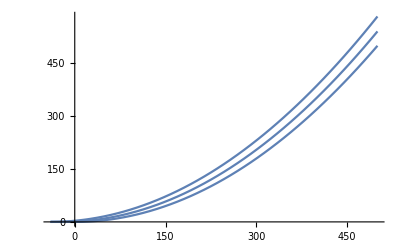

```mathematica
explosionFactors=Table[k*1.0,{k,maxExplosionFactor,(-layers+1)*delayFactor,-(maxExplosionFactor+(layers-1)*delayFactor)/(frameCount-1)}];
explosionFactors
Plot[Table[getNonlinearFactor[linear,layer ],{layer,3}],{linear,-2 delayFactor,maxExplosionFactor}]
```

{100.,88.5556,77.1111,65.6667,54.2222,42.7778,31.3333,19.8889,8.44444,-3.}

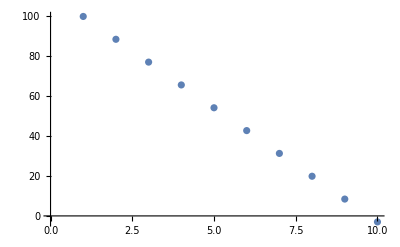

```mathematica
explosionFactors=Table[k*1.0,{k,maxExplosionFactor,(-layers+1)*delayFactor,-(maxExplosionFactor+(layers-1)*delayFactor)/(frameCount-1)}];
explosionFactors
ListPlot[explosionFactors]
```

```mathematica
(Exp[x]-1)/2+(-layers+1)*delayFactor/.x->5.
```

70.7066

```mathematica
D[(x^2-1)/2,x]/.x->1
```

1

{439.,364.689,298.987,241.2,190.667,146.753,108.854,76.3924,48.8225,25.6261,6.31421,-9.5732,-22.4671,-32.7694,-40.8532,-47.0624,-51.7121,-55.0881,-57.4476,-59.0186,-60.}

{{385.442,265.997,178.786,116.355,72.7079,43.073,23.6982,11.6716,4.76728,1.3134,0.0797386,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{439.922,311.559,216.465,147.099,97.388,62.4834,38.5607,22.6387,12.426,6.18853,2.63744,0.834508,0.11349,0.004,0.004,0.004,0.004,0.004,0.004,0.004,0.004},{498.002,360.722,257.743,181.443,125.668,85.4938,57.0231,37.2058,23.6847,14.6637,8.79515,5.08572,2.81744,1.48301,0.7332,0.334762,0.13738,0.0482531,0.0130292,0.004,0.004}}

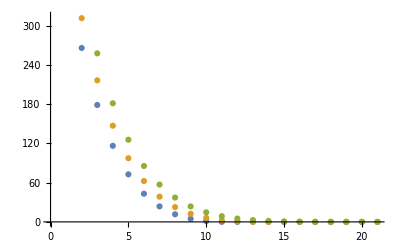

```mathematica
maxExplosionFactor=500;
layers=3;
delayFactor=30;
frameCount=20;
kExponent=4;
getNonlinearFactor[linear_,layer_]:=Module[{layerOffset,linearOffset,returnValue},minFactor=0.004;
layerOffset=If[layer>1,layer-1,0];
linearOffset=linear+layerOffset*delayFactor;
returnValue=linearOffset^2/maxExplosionFactor;
(*If[returnValue>maxExplosionFactor,returnValue=maxExplosionFactor];*)If[linearOffset<0||returnValue<minFactor,returnValue=minFactor];
returnValue];
maxk=maxExplosionFactor^(1/kExponent);
explosionFactors=Table[(k^kExponent-1.)+(-layers+1)*delayFactor,{k,maxk,1,-(maxk-1)/frameCount}];
explosionFactors
Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}]
ListPlot[Table[getNonlinearFactor[explosionFactors[[fid]],layer ],{layer,layers},{fid,Length[explosionFactors]}]]
```

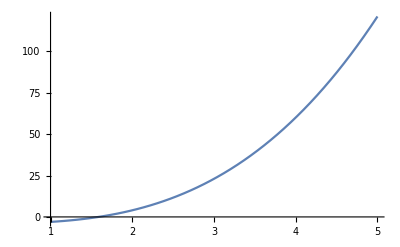

```mathematica
Plot[(x^3-1)+(-layers+1)*delayFactor,{x,1,5}]
```

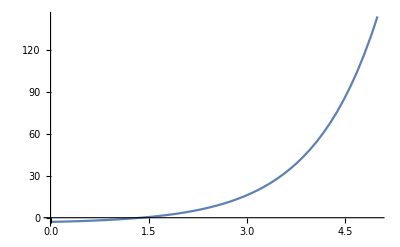

```mathematica
Plot[Exp[x]-1+(-layers+1)*delayFactor,{x,0,5}]
```

```mathematica
ArgMin[3,1,2]
```

ArgMin::ivar: 2 is not a valid variable.

ArgMin[3,1,2]

```mathematica
Ordering[{3,1,2,4},1]
```

{2}